# Building A30

One of the two central functions in AntCalc is BuildAntenna. This function builds, from the Feynman diagrams, the unintegrated antenna functions. 

Start by launching AntCalc:

```mathematica
<<AntCalc`
```

AntCalc 0.2.0 α 1

FeynCalc 10.2.1  ·  FeynArts 3.12 (27 Mar 2025)  ·  FeynHelpers 2.0.0  ·  FeynCalcLegacy 1.0.0

LiteRed2 2.025β

Building an antenna in AntCalc is remarkably simple. Simply run:

```mathematica
A30unintegrated = BuildAntenna[A,3,0]
```

[2026-07-20 14:43:36] BuildAntenna [1/5]: resolving route setup {A, 3, 0} with Component -> All, Contribution -> All

[2026-07-20 14:43:36] BuildAntenna [2/5]: building route data {A, 3, 0} with Component -> All, Contribution -> All

[2026-07-20 14:43:36] BuildAntenna [3/5]: extracting public result {A, 3, 0} with Component -> All, Contribution -> All

[2026-07-20 14:43:36] BuildAntenna [4/5]: building diagnostics {A, 3, 0} with Component -> All, Contribution -> All

[2026-07-20 14:43:36] BuildAntenna [5/5]: formatting public return {A, 3, 0} with Component -> All, Contribution -> All

-(2 ε)/q2+(2 s12^2)/(q2 s13 s23)+(2 s12)/(q2 s13)+(2 s12)/(q2 s23)-(ε s23)/(q2 s13)-(ε s13)/(q2 s23)+s23/(q2 s13)+s13/(q2 s23)

This function builds the antennae specifically with the two hard original radiators as particles 1 and 2, that is, in this case A30(1q, 3g, 2bar q). In our notation, q2 denotes the centre of mass energy, which for this case makes q2 = s123 = s12 + s13 + s23. These antenna functions are most commonly shown as epsilon expansions, and that effect can be achieved here with:

```mathematica
A30Epsilon = A30unintegrated//Collect[#,Epsilon]&
```

(2 s12^2)/(q2 s13 s23)+(2 s12)/(q2 s13)+(2 s12)/(q2 s23)+ε (-s13/(q2 s23)-s23/(q2 s13)-2/q2)+s23/(q2 s13)+s13/(q2 s23)

There are several options for this function, that may become useful as it is used. 

We are able to inspect the diagrams that led to this antenna by running:

[2026-07-20 14:56:02] BuildAntenna [1/5]: resolving route setup {A, 3, 0} with Component -> All

[2026-07-20 14:56:02] BuildAntenna [2/5]: building route data {A, 3, 0} with Component -> All

[AntCalc] Tree diagrams: A3 (3 final-state partons)

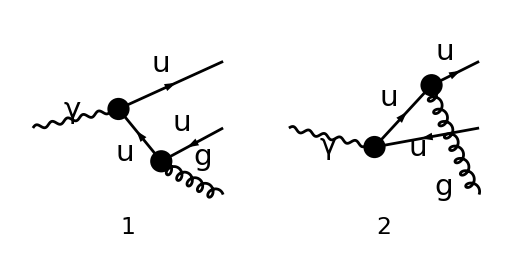

FeynArtsGraphics()(([1] | [2]))

[2026-07-20 14:56:09] BuildAntenna [3/5]: extracting public result {A, 3, 0} with Component -> All

[2026-07-20 14:56:09] BuildAntenna [4/5]: building diagnostics {A, 3, 0} with Component -> All

[2026-07-20 14:56:09] BuildAntenna [5/5]: formatting public return {A, 3, 0} with Component -> All

-(2 ε)/q2+(2 s12^2)/(q2 s13 s23)+(2 s12)/(q2 s13)+(2 s12)/(q2 s23)-(ε s23)/(q2 s13)-(ε s13)/(q2 s23)+s23/(q2 s13)+s13/(q2 s23)

```mathematica
A30Diagrams=BuildAntenna[A,3,0,printDiagram->True]
```

we can also check the intermediate steps that AntCalc walked through to get to this final expression by running,

```mathematica
{A30ant,A30InterSteps}=BuildAntenna[A,3,0,IntermediateSteps->True]
```

[2026-07-20 15:07:33] BuildAntenna [1/5]: resolving route setup {A, 3, 0} with Component -> All

[2026-07-20 15:07:33] BuildAntenna [2/5]: building route data {A, 3, 0} with Component -> All

[2026-07-20 15:07:33] BuildAntenna [3/5]: extracting public result {A, 3, 0} with Component -> All

[2026-07-20 15:07:33] BuildAntenna [4/5]: building diagnostics {A, 3, 0} with Component -> All

[2026-07-20 15:07:33] BuildAntenna [5/5]: formatting public return {A, 3, 0} with Component -> All

{-(2 ε)/q2+(2 s12^2)/(q2 s13 s23)+(2 s12)/(q2 s13)+(2 s12)/(q2 s23)-(ε s23)/(q2 s13)-(ε s13)/(q2 s23)+s23/(q2 s13)+s13/(q2 s23),<|Amplitude→T_Col2Col3^Glu4 (((φ(k_1)).(γ·ε^*(k_3)).(γ·(k_1+k_3)).(γ·ε(p)).(φ(-k_2)))/(k_1+k_3)^2-((φ(k_1)).(γ·ε(p)).(γ·(k_2+k_3)).(γ·ε^*(k_3)).(φ(-k_2)))/(k_2+k_3)^2),Interference→(4 (ε-1) (N^2-1) (-2 s12^2-2 s12 (s13+s23)+(ε-1) s13^2+2 ε s13 s23+(ε-1) s23^2))/(s13 s23),Antenna→-(2 ε)/q2+(2 s12^2)/(q2 s13 s23)+(2 s12)/(q2 s13)+(2 s12)/(q2 s23)-(ε s23)/(q2 s13)-(ε s13)/(q2 s23)+s23/(q2 s13)+s13/(q2 s23)|>}

The steps are given in terms of an association and each of the steps can be accessed directly:

```mathematica
A30Amp=A30InterSteps["Amplitude"]
```

T_Col2Col3^Glu4 (((φ(k_1)).(γ·ε^*(k_3)).(γ·(k_1+k_3)).(γ·ε(p)).(φ(-k_2)))/(k_1+k_3)^2-((φ(k_1)).(γ·ε(p)).(γ·(k_2+k_3)).(γ·ε^*(k_3)).(φ(-k_2)))/(k_2+k_3)^2)

We can also use and reform a number of stored results in AntCalc’s cache system. Those stored results are accessed with

```mathematica
A30Stored=BuildAntenna[A,3,0,UseStoredResults->True]
```

[2026-07-20 15:11:03] BuildAntenna [1/5]: resolving route setup {A, 3, 0} with Component -> All

[2026-07-20 15:11:03] BuildAntenna [2/5]: building route data {A, 3, 0} with Component -> All

[2026-07-20 15:11:03] BuildAntenna [3/5]: extracting public result {A, 3, 0} with Component -> All

[2026-07-20 15:11:03] BuildAntenna [4/5]: building diagnostics {A, 3, 0} with Component -> All

[2026-07-20 15:11:03] BuildAntenna [5/5]: formatting public return {A, 3, 0} with Component -> All

-(2 ε)/q2+(2 s12^2)/(q2 s13 s23)+(2 s12)/(q2 s13)+(2 s12)/(q2 s23)-(ε s23)/(q2 s13)-(ε s13)/(q2 s23)+s23/(q2 s13)+s13/(q2 s23)

and the results can be reformed using

```mathematica
A30Restore=BuildAntenna[A,3,0,StoreResults->True]
```

[2026-07-20 15:14:51] BuildAntenna [1/5]: resolving route setup {A, 3, 0} with Component -> All

[2026-07-20 15:14:51] BuildAntenna [2/5]: building route data {A, 3, 0} with Component -> All

[2026-07-20 15:14:51] BuildAntenna [3/5]: extracting public result {A, 3, 0} with Component -> All

[2026-07-20 15:14:51] BuildAntenna [4/5]: building diagnostics {A, 3, 0} with Component -> All

[2026-07-20 15:14:51] BuildAntenna [5/5]: formatting public return {A, 3, 0} with Component -> All

-(2 ε)/q2+(2 s12^2)/(q2 s13 s23)+(2 s12)/(q2 s13)+(2 s12)/(q2 s23)-(ε s23)/(q2 s13)-(ε s13)/(q2 s23)+s23/(q2 s13)+s13/(q2 s23)

Finally, A30 also presents with an experimental massive route, the only one of its kind so far. It is called and works in the exact same way

```mathematica
mA30unintegrated=BuildAntenna[A,3,0,quarkMass->mQ]
```

[2026-07-20 15:17:22] BuildAntenna [1/5]: resolving route setup {A, 3, 0} with Component -> All

[2026-07-20 15:17:22] BuildAntenna [2/5]: building route data {A, 3, 0} with Component -> All

[2026-07-20 15:17:25] BuildAntenna [3/5]: extracting public result {A, 3, 0} with Component -> All

[2026-07-20 15:17:25] BuildAntenna [4/5]: building diagnostics {A, 3, 0} with Component -> All

[2026-07-20 15:17:25] BuildAntenna [5/5]: formatting public return {A, 3, 0} with Component -> All

(-8 mQ^4 (s13^2+s23^2)-2 mQ^2 (s12 (s13^2-4 s13 s23+s23^2)+s13^3+s13^2 s23+s13 s23^2+s23^3)+s13 s23 (2 s12^2+2 s12 (s13+s23)+s13^2+s23^2))/(4 s13^2 s23^2 (4 mQ^2+s12+s13+s23))